```mathematica
v1={0.00010963510637404513,0.0002118056948673042,0.00046606583518157905,0.0030450567629931595,0.043512540856572086,0.5922375617921545,6.707914};
v2={0.026969227611174353,0.19358426484035307,47.214301509694515};
v3={0.00007184578349226491,0.00005178494784182731,0.00014835687760091066,0.0017844813107656709,0.023759960438165972,0.3703524175639614,4.617639};
```

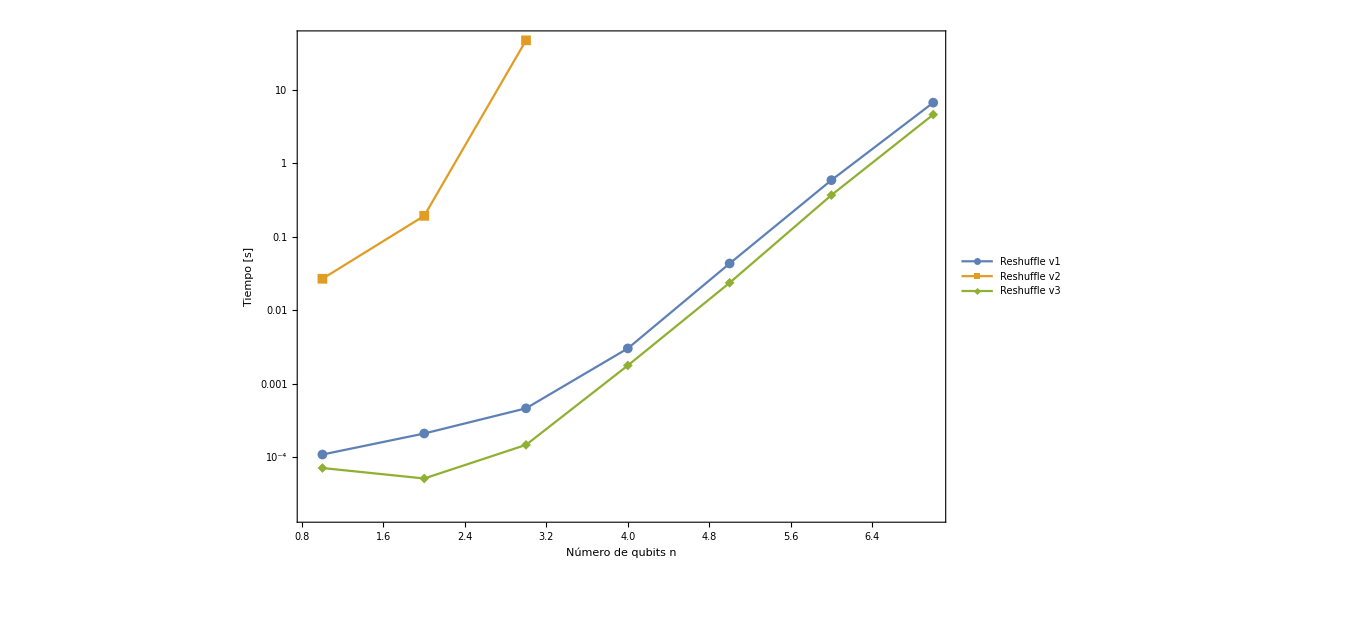

```mathematica
tiempos=ListLogPlot[{v1,v2,v3},PlotStyle->PointSize[Medium],PlotRange->All,PlotLegends->{Style["Reshuffle v1","Text"],Style["Reshuffle v2","Text"],Style["Reshuffle v3","Text"]},ImageSize->1000,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{Style["Tiempo [s]",Bold,Black,25],None},{Style["Número de qubits n",Bold,Black,25],None}},FrameTicks->All,Joined->True,PlotMarkers->{Automatic,Medium}]
```

```mathematica
FindFit[v3,a b^x,{a,b},x]
Table[a b^x/.%,{x,7}]
v3
```

{a→9.684×10^-8,b→12.5}

{1.2105×10^-6,0.0000151312,0.00018914,0.00236425,0.0295532,0.369414,4.61768}

{0.0000718458,0.0000517849,0.000148357,0.00178448,0.02376,0.370352,4.61764}

```mathematica
h[x_]:=2.7544764994393287*^-7 11.355907108259919^x
```

```mathematica
l[x_]:=9.684000231231061*^-8 12.499994402080334^x
```

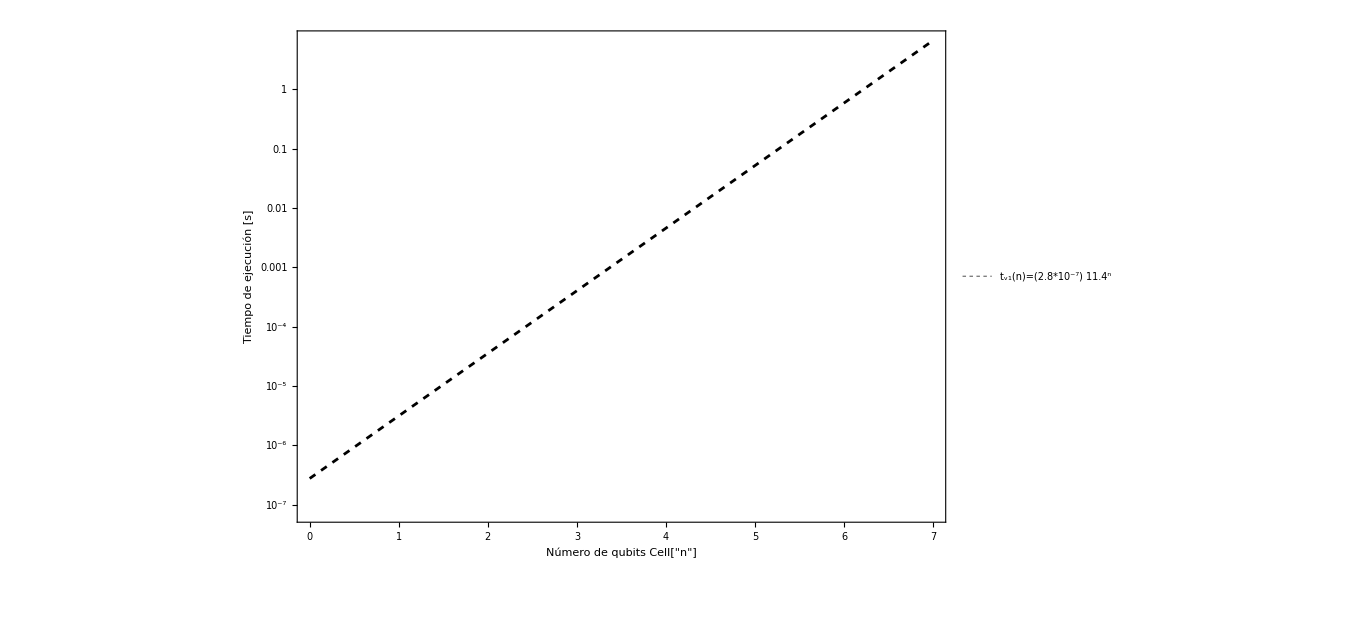

```mathematica
t=ListLogPlot[Table[{i,h[i]},{i,0,7,0.1}],Joined->True,PlotRange->All,PlotStyle->{Black,Dashed,Thickness[0.002]},PlotLegends->{Style["t_v1(n)=(2.8*10^-7) 11.4^n","Text"],Style["Reshuffle v1","Text"],Style["Reshuffle v2","Text"]},PlotStyle->PointSize[Medium],AxesLabel->{Style["Número de qubits Cell["n",ExpressionUUID->"753d6213-c7bf-441e-a126-8463b232edd9"]",Medium,Bold,Black],Style["Memoria RAM [Bytes]",Medium,Bold,Black]},ImageSize->1000,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{Style["Tiempo de ejecución [s]",Bold,Black,25],None},{Style["Número de qubits Cell["n",ExpressionUUID->"ba376798-38a7-4dca-8d1b-b7246f4e8f55"]",Bold,Black,25],None}},FrameTicks->All]
```

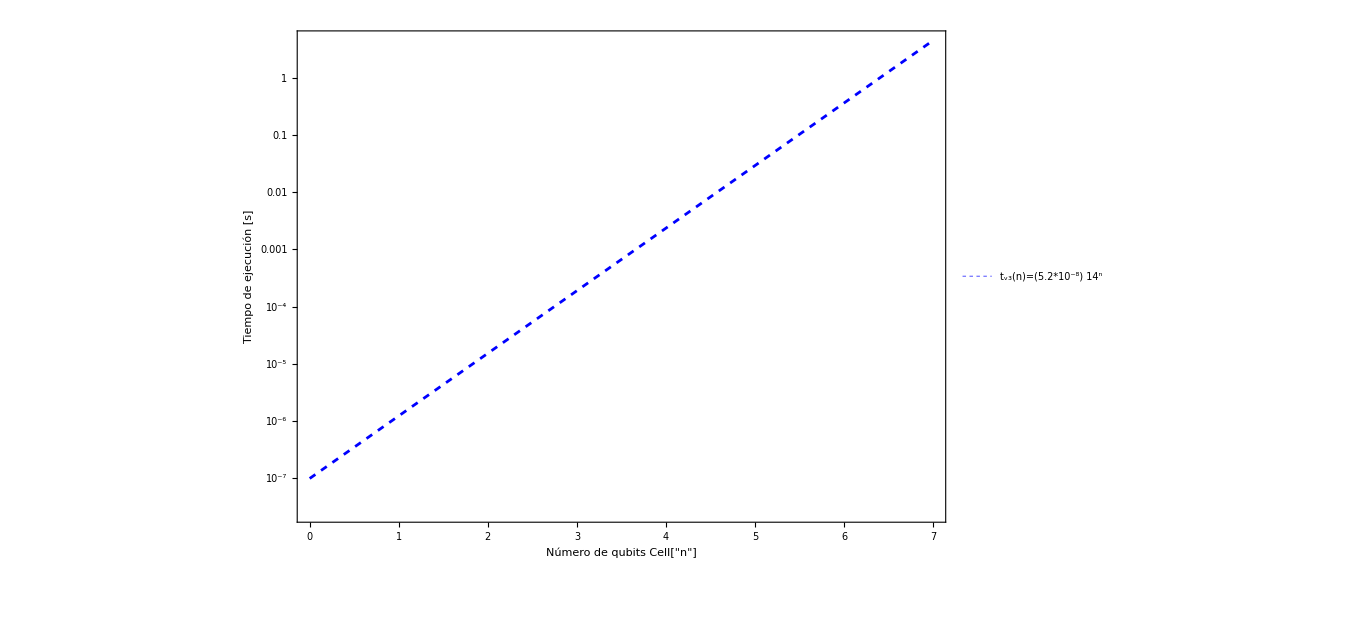

```mathematica
t3=ListLogPlot[Table[{i,l[i]},{i,0,7,0.1}],Joined->True,PlotRange->All,PlotStyle->{Blue,Dashed,Thickness[0.002]},PlotLegends->{Style["t_v3(n)=(5.2*10^-8) 14^n","Text"],Style["Reshuffle v1","Text"],Style["Reshuffle v2","Text"]},PlotStyle->PointSize[Medium],AxesLabel->{Style["Número de qubits Cell["n",ExpressionUUID->"ace2dd4c-c0ea-400f-acd5-5cc6e16d1a5c"]",Medium,Bold,Black],Style["Memoria RAM [Bytes]",Medium,Bold,Black]},ImageSize->1000,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{Style["Tiempo de ejecución [s]",Bold,Black,25],None},{Style["Número de qubits Cell["n",ExpressionUUID->"7fba7705-0636-4f90-9319-64b8ac09cdc4"]",Bold,Black,25],None}},FrameTicks->All]
```